## Config

Source folder for JPG files:

```mathematica
imageDir="/media/superraid/images/images/";
```

Nr of raw files:

```mathematica
nrRawFiles=FileNames["*.CR2",imageDir,∞]//Length
```

9981

```mathematica
jpgFileNames=FileNames["*.jpg"|"*.JPG",imageDir,∞];
```

Number of images found:

```mathematica
nrJpgFiles=Length[jpgFileNames]
```

3955

Folder for local data storage:

```mathematica
dataDir=FileNameJoin[{NotebookDirectory[],"dataStorage"}]
```

/home/malte/dev/imStat/dataStorage

```mathematica
CreateDirectory[dataDir]
```

/home/malte/dev/imStat/dataStorage

## Retrieve mini JPG files and basic data

Compute data file name from original path, making sure that no collisions will occur:

```mathematica
(Union[Hash[#,"CRC32"]&/@jpgFileNames]//Length)==nrJpgFiles
```

True

```mathematica
storageFile[path_]:=FileNameJoin[{dataDir,ToString[Hash[path,"CRC32"]]<>".dst"}];
```

```mathematica
storageFileImg[path_]:=FileNameJoin[{dataDir,ToString[Hash[path,"CRC32"]]<>".jpg"}];
```

Fetch original image and save data into data file:

```mathematica
createData[path_]/;FileExistsQ[storageFile[path]]=Null;
```

```mathematica
createData[path_]:=Module[{img,dimensions,smallImg,aperture,bitDepth,orientation,colorSpace,date,exposure,focalLength,imageSize,iso,manufacturer,model,exifData},
exifData=Import[path,{{"Aperture","BitDepth","CameraTopOrientation","ColorSpace","Date","Exposure","FocalLength","ImageSize","ISOSpeed","Manufacturer","Model"}}];
If[!MatchQ[exifData,{_,_,_,_String,{_,_,_,_,_,_},_,_,{_,_},_,_String,_String}],
Return[$Failed];
];
img=Import[path];
dimensions=ImageDimensions[img];
smallImg=ImageResize[img,{300},Resampling->"Bilinear"];
Put[{dimensions,exifData},storageFile[path]];
Export[storageFileImg[path],smallImg];
]
```

File size:

```mathematica
fileSizes={#,FileByteCount[#]}&/@jpgFileNames;
```

```mathematica
Put[fileSizes,FileNameJoin[{dataDir,"fileSizes.dst"}]];
```

Retrieving file sizes:

```mathematica
fileSizes=Get[FileNameJoin[{dataDir,"fileSizes.dst"}]];
```

Fetch data in order of preference {memory, data file}:

```mathematica
ClearAll[getData];
getData[path_]/;FileExistsQ[storageFile[path]]:=getData[path]={Import[storageFileImg[path]],Get[storageFile[path]]}
```

```mathematica
getData[_]:=$Failed
```

Accessor functions for properties:

```mathematica
getData[path_,"Date"]:=getData[path][[2,2,5]]
```

## Retrieve image data

```mathematica
Monitor[
ParallelDo[createData[jpgFileNames[[i]]],{i,Length[jpgFileNames]}],
Refresh[
ProgressIndicator[Length@FileNames["*",dataDir],{0,2Length[jpgFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
]
```

Import::fmterr: Cannot import data as "JPEG" format.

General::stop: Further output of Import :: fmterr will be suppressed during this calculation.

Import::fmterr: Cannot import data as "JPEG" format.

General::stop: Further output of Import :: fmterr will be suppressed during this calculation.

Import::fmterr: Cannot import data as "JPEG" format.

General::stop: Further output of Import :: fmterr will be suppressed during this calculation.

Import::fmterr: Cannot import data as "JPEG" format.

General::stop: Further output of Import :: fmterr will be suppressed during this calculation.

```mathematica
goodFileNames=Select[jpgFileNames,FileExistsQ[storageFile[#]]&&FileExistsQ[storageFileImg[#]]&];
```

## Number of images taken

```mathematica
Length[goodFileNames]
```

3683

## Images taken over time

```mathematica
getData[goodFileNames[[1]],"Date"]
```

{2007,12,23,17,14,56}

```mathematica
imageDates=Monitor[
Table[getData[goodFileNames[[i]],"Date"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
Tally@Cases[imageDates,{y_,mo_,d_,h_,mi_,s_}]
```

{{{2007,12,23,17,14,56},1},{{2007,12,23,18,51,17},2},{{2007,12,23,18,51,48},1},{{2007,12,24,22,12,43},1},{{2007,12,25,13,38,44},1},«3189»,{{2007,9,23,13,38,54},1},{{2007,9,23,13,39,26},1},{{2007,9,23,13,39,36},1},{{2007,9,23,13,40,6},1},{{2007,9,24,16,2,27},1}}

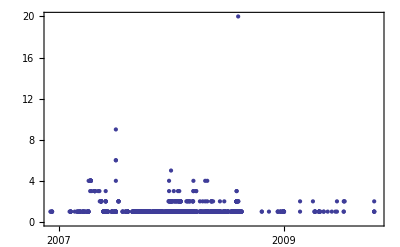

```mathematica
DateListPlot@Tally[Cases[imageDates,{y_,mo_,d_,h_,mi_,s_}]]
```

## Image colors over time

## Orientations

## Camera models

## Aperture

## Bit depth

## Color space

## Time of day taken

## Exposure

## Focal length

## Image size

## ISO

## Memory used

```mathematica
Total@fileSizes[[All,2]]
```

6114153844

## Flash